```mathematica
M[w_,x_,y_]:=w.x*y+w.x(y-1)
L[m_]:=Log[1+Exp[-m]]
dL[m_]:=-ⅇ^-m/(1+ⅇ^-m)
Q[w_]:=Sum[L[M[w,X[[i]],Y[[i]]]],{i,1,Length[X]}]
```

```mathematica
D[M[{w1,w2,w3},{x1,x2,x3},y],w1]//Simplify
```

x1 (-1+2 y)

```mathematica
x1x2=Flatten@{1,Table[#1^(i-j)*#2^j,{i,1,6},{j,0,i}]}&[x1,x2];
```

```mathematica
Y=data[[;;,3]];
XX=Table[Flatten@{1,data[[i,{1,2}]]},{i,1,Length[data]}];
```

```mathematica
X=Table[Flatten@{1,Table[(data[[k]][[1]])^(i-j)*(data[[k]][[2]])^j,{i,1,6},{j,0,i}]},{k,1,Length[data]}];
```

```mathematica
GradDecent[X_,Y_,a_,λ_,maxiter_]:=Module[{w=RandomReal[{-.1,.1},Length[X[[1]]]],m=Length[X],i,j,k,t1={},t2={},w1},
AppendTo[t1,w];
For[i=1,i≤maxiter,i++,
w1=w(1-a λ/m)-a/m Sum[dL[M[w,X[[j]],Y[[j]]]](2Y[[j]]-1)X[[j]],{j,1,m}];
w=w1;
AppendTo[t1,w];];
{w,t1}]
```

```mathematica
StochasticGrad[X_,Y_,a_,λ_,maxiter_]:=Module[{w=RandomReal[{-.1,.1},Length[X[[1]]]],m=Length[X],i,j,k,t1={},t2={},w1},
AppendTo[t1,w];
For[i=1,i≤maxiter,i++,
k=RandomInteger[{1,m}];
w1=w(1-a λ/m)-a/m dL[M[w,X[[k]],Y[[k]]]](2Y[[k]]-1)X[[k]];
w=w1;
AppendTo[t1,w];];
{w,t1}]
```

{9.25,Null}

0.221026

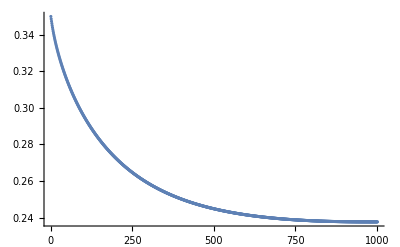

```mathematica
Timing[d1=GradDecent[X,Y,.2,0.1,1000];]
Q[d1[[1]],0.1]
ListPlot[Table[Q[d1[[2]][[i]],0.2],{i,1,Length[d1[[2]]]}]]
```

{2.46875,Null}

0.31533

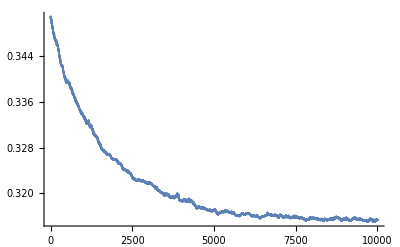

```mathematica
Timing[d2=StochasticGrad[X,Y,.5,.1,100000];]
Q[d2[[1]],.1]
ListPlot[Table[Q[d2[[2]][[i]],.1],{i,1,Length[d2[[2]]]}]]
```

```mathematica
d1=NArgMin[Q1[Table[x[i],{i,0,27}],1],Table[x[i],{i,0,27}],MaxIterations->1000,AccuracyGoal->4]
```

```mathematica
Q[d1]
```

60.5374

```mathematica
Q[d[[1]]]
```

42.0977

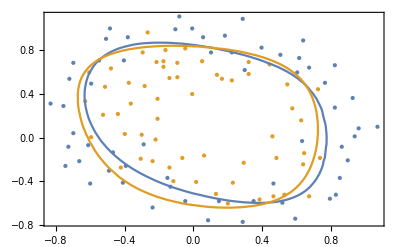

```mathematica
Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Axes->False,Frame->True,ImageSize->400],ContourPlot[Evaluate[{d[[1]].x1x2==0,d1.x1x2==0}],{x1,-2,2},{x2,-2,2}]]
```